# 3D Gibbs-ensemble Monte Carlo

12/24/2023
GEMC with periodic condition.
latvec1(2) is the number of atoms and {x,y,z} length of box1(2) respectively .
numb1(2)={atom1,atom2,......} is the type and number of atoms in box1(2).
sigma and epsilon ={parameter of atom1,parameter of atom2,......} with angstrom and J unit respectively.
b is that  temperature times Boltzmann constant with J unit

```mathematica
numb1={651};
numb2={651};
latvec1={50,50,50};
latvec2={50,50,50};
sigma={3.401};
epsilon={0.978638}*1000/(6.022140857*10^23);
b=1.3806485279*10-23*150.687;
cutoff=10;
config1=Table[RandomReal[],#,3]&/@numb1*latvec1[[1]]-latvec1[[1]]/2;

config2=Table[RandomReal[],#,3]&/@numb2*latvec2[[1]]-latvec2[[1]]/2;

configEpbc[config_,cutoff_,latvec_,epsilon_,sigma_]:=Module[{dist,utot},dist=Flatten[Table[If[i==j&&k==l &&a==b==c==0,Nothing,{i,j,EuclideanDistance[config[[i,k]],config[[j,l]]+{a,b,c}*latvec]}],{i,Length[config]},{j,Length[config]},{k,Length[config[[i]]]},{l,Length[config[[j]]]},{a,-1,1},{b,-1,1},{c,-1,1}],6];
utot=Sum[If[i[[3]]>cutoff,0,4*((epsilon[[i[[1]]]]+epsilon[[i[[2]]]])^0.5)*(((sigma[[i[[1]]]]+sigma[[i[[2]]]])/(i[[3]]))^12-((sigma[[i[[1]]]]+sigma[[i[[2]]]])/(i[[3]]))^6)],{i,dist}];
N[utot/2]];

randmove[stepleng_]:=Module[{localConfig={config1,config2},cho0,cho,cho1,cho2,oldE,temp,newE,lat={latvec1,latvec2}},
cho0=RandomInteger[{1,2}];
cho=RandomInteger[{1,Length[localConfig[[cho0]]]}];
cho1=RandomInteger[{1,Length[localConfig[[cho0]][[cho]]]}];
cho2=Table[RandomReal[{-1,1}]*stepleng/100,3]*lat[[cho0]];
oldE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
localConfig[[cho0]][[cho]][[cho1]]=localConfig[[cho0]][[cho]][[cho1]]+cho2;

temp=MapThread[#1>#2&,{lat[[cho0]],localConfig[[cho0]][[cho]][[cho1]]}];
localConfig[[cho0]][[cho]][[cho1]]=MapThread[If[#1,#2,#2-#3]&,{temp,localConfig[[cho0]][[cho]][[cho1]],lat[[cho0]]}];
newE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
If[RandomReal[]<N[Exp[-(1/b)*(newE-oldE)]],localConfig,{config1,config2}]
];

volchange[length_]:=Module[{cho,oldE,lat1=latvec1,lat2=latvec2,con1=config1,con2=config2,newE},
cho=RandomReal[{-1,1}]*length;
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con1=con1*(lat1[[1]]-cho)/lat1[[1]];
con2=con2*(lat2[[1]]+cho)/lat2[[1]];
lat1=lat1+cho;
lat2=lat2-cho;
newE=configEpbc[con1,cutoff,lat1,epsilon,sigma]+configEpbc[con2,cutoff,lat2,epsilon,sigma];
If[RandomReal[]<Exp[-(1/b)*(newE-oldE)]*((lat1[[1]]^(3*Total[numb1]))*(lat2[[1]]^(3*Total[numb2])))/((latvec1[[1]]^(3*Total[numb1]))*(latvec2[[1]]^(3*Total[numb2]))),{con1,con2,lat1,lat2},{config1,config2,latvec1,latvec2}]
];

den:=(
{numb1[[1]]/latvec1[[1]]^3,numb2[[1]]/latvec2[[1]]^3})
paraexchange[]:=Module[{num,con,cho,cho1,cho2,oldE,lat,newE},
num={numb1,numb2};
con={config1,config2};
lat={latvec1,latvec2};
cho=RandomInteger[{1,2}];
cho1=RandomInteger[{1,Length[con[[cho]]]}];
cho2=RandomInteger[{1,Length[con[[cho]][[cho1]]]}];
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con[[3-cho]][[cho1]]=Append[con[[3-cho]][[cho1]],Table[RandomReal[{-1,1}],3]*lat[[3-cho]]];
con[[cho]][[cho1]]=Delete[con[[cho]][[cho1]],cho2];
newE=configEpbc[con[[1]],cutoff,lat[[1]],epsilon,sigma]+configEpbc[con[[2]],cutoff,lat[[2]],epsilon,sigma];
num[[cho]][[cho1]]=num[[cho]][[cho1]]-1;
num[[3-cho]][[cho1]]=num[[3-cho]][[cho1]]+1;
If[RandomReal[]<N[N[Exp[-(1/b)*(newE-oldE)]]*((Total[num[[cho]]]+1)*lat[[3-cho]][[1]]^3)/(Total[num[[3-cho]]]*lat[[cho]][[1]]^3)],{con[[1]],con[[2]],num[[1]],num[[2]]},{config1,config2,numb1,numb2}]
];
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
conE={};
densi={};
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[];conE=Append[conE,configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]];densi=Append[densi,den],10];
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
```

1.32804×10^-8

{}

{}

51

53

{51}

{53}

{97.5905,97.5905,97.5905}

{102.409,102.409,102.409}

1.61281×10^-8

```mathematica
ListPointPlot3D[config2[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]]}]
ListPointPlot3D[config1[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]]}]
```

Automatic::prng: Value of option PlotRange -> {-102.409,102.409,-102.409,102.409,-102.409,102.409} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

Automatic::prng: Value of option PlotRange -> {-97.5905,97.5905,-97.5905,97.5905,-97.5905,97.5905} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

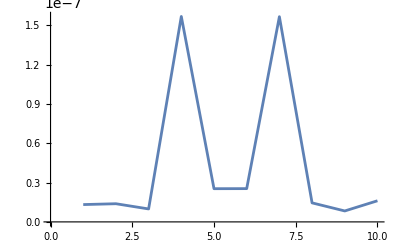

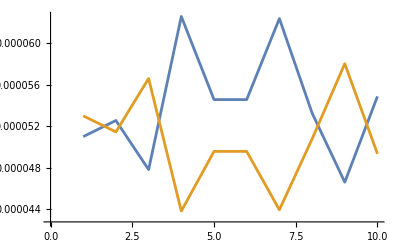

```mathematica
ListLinePlot[conE]
ListLinePlot[{Transpose[densi][[1]],Transpose[densi][[2]]}]
```

```mathematica
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[],50];
```

{100,100,100}

-Graphics3D-

```mathematica
N[(8075+2354)]/16
```

651.813